```mathematica
daughter227=Import["C:\\Users\\mxy\\Desktop\\Modeling paper\\iptg1mmrawtxt.txt","Table"]
```

{{CellID,MotherID,Time(Frames),Cellage,Longaxis(L),Area,Fluor1sum,Fluor1mean,Fluor2sum,Fluor2mean},{1,0,0.0166667,87,13,77,260132,2531.34,113581,279.078},164509,{16416,13255,6.66667,4,12,72,324926,3665.86,112243,362.931},{16416,13255,6.68333,4,12,78,358606,3750.51,123412,386.205}}
 |  |  |  |

```mathematica
Length[daughter227]
```

164513

```mathematica
daughter227[[2;;Length[daughter227],{7}]]=N[(daughter227[[2;;Length[daughter227],{8}]])*daughter227[[2;;Length[daughter227],{6}]]];
```

```mathematica
daughter227[[2;;Length[daughter227],{9}]]=N[(daughter227[[2;;Length[daughter227],{10}]])*daughter227[[2;;Length[daughter227],{6}]]];
```

```mathematica
daughter227[[2;;Length[daughter227],{8}]]=N[(daughter227[[2;;Length[daughter227],{8}]])*daughter227[[2;;Length[daughter227],{6}]]/10258];
```

```mathematica
daughter227[[2;;Length[daughter227],{10}]]=N[(daughter227[[2;;Length[daughter227],{8}]])*daughter227[[2;;Length[daughter227],{6}]]/10258];
```

```mathematica
MatrixForm[daughter227[[1;;5]]]
```

(CellID | MotherID | Time(Frames) | Cellage | Longaxis(L) | Area | Fluor1sum | Fluor1mean | Fluor2sum | Fluor2mean
1 | 0 | 0.0166667 | 87 | 13 | 77 | 194913. | 19.0011 | 21489. | 0.142628
1 | 0 | 0.0333333 | 87 | 14 | 83 | 209188. | 20.3927 | 21896. | 0.165002
1 | 0 | 0.05 | 87 | 14 | 80 | 202412. | 19.7321 | 17591. | 0.153887
1 | 0 | 0.0666667 | 87 | 13 | 83 | 204246. | 19.9109 | 21626. | 0.161104)

```mathematica
daughter227data=momdaughtconnect[daughter227];//AbsoluteTiming
```

{104.332,Null}

```mathematica
Length[daughter227data]
```

450

```mathematica
MatrixForm[daughter227data[[1;;5]]]
```

(parent | d1 | d2 | motherfl | d1fl | d2fl | motherfl2 | d1fl2 | d2fl2 | dmean | rootntot/2
20 | 848 | 849 | 452467. | 106267. | 288375. | 44577. | 14327. | 30050. | 197321. | 336.328
654 | 879 | 880 | 711370. | 337971. | 323237. | 57960. | 26025. | 27761. | 330604. | 421.714
159 | 885 | 886 | 712460. | 334873. | 319501. | 58832. | 29877. | 28320. | 327187. | 422.037
49 | 923 | 924 | 881592. | 434023. | 452660. | 47721. | 27055. | 22868. | 443342. | 469.466)

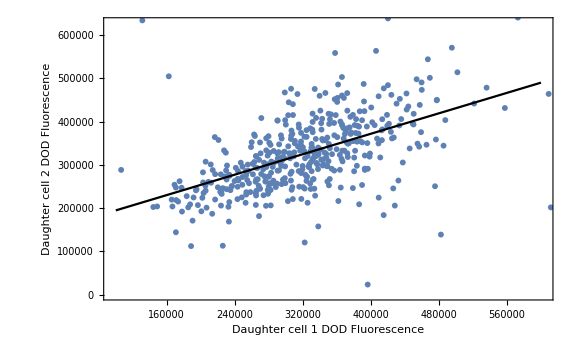

```mathematica
Show[ListPlot[
Transpose@{daughter227data[[All,5]],daughter227data[[All,6]]},
ImageSize-> Large,Frame->True,LabelStyle->Directive[Black,Medium],
FrameLabel->{"Daughter cell 1 DOD Fluorescence","Daughter cell 2 DOD Fluorescence"}],Plot[lm[x],{x,100000,600000},PlotStyle->Black]]
```

```mathematica
data=Map[{daughter227data⟦#,5⟧,daughter227data⟦#,6⟧}&,Range[2,450]];
```

```mathematica
lm=LinearModelFit[data,x,x]
```

FittedModel[135561.+0.591037 x]

```mathematica
N[Correlation[data[[All,1]],data[[All,2]]]]
```

0.532032

```mathematica
PairedTTest[{data[[All,1]],data[[All,2]]}]
```

0.332053

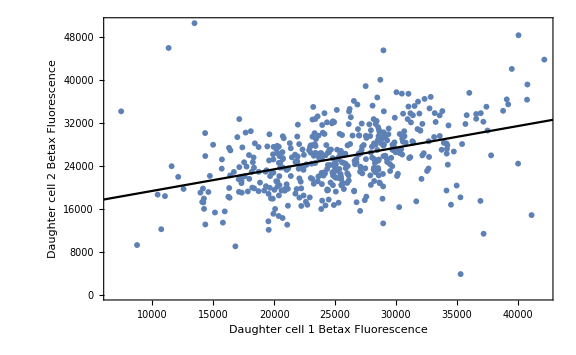

```mathematica
Show[ListPlot[
Transpose@{daughter227data[[All,8]],daughter227data[[All,9]]},
ImageSize-> Large,Frame->True,LabelStyle->Directive[Black,Medium],
FrameLabel->{"Daughter cell 1 Betax Fluorescence","Daughter cell 2 Betax Fluorescence"}],Plot[lmb[x],{x,0,45000},PlotStyle->Black]]
```

```mathematica
olks500=metabgensteadystate[10,0,2.1,0,0,0,0,0,0,0,0,14,0.02];//AbsoluteTiming
```

{3242.99,Null}

```mathematica
olks500kill=mxcontkilling[10,olks500[[1]],0,2.1,0,0,0,0,0,0,0,0,14,0.02];//AbsoluteTiming
```

{44060.2,Null}

```mathematica
olks500typ=titeryieldproductivity[olks500kill];
```

```mathematica
ListLinePlot[{olks500typ[[1]],olks500typ[[3]]},PlotStyle->{{Thickness[0.008],RGBColor[1,0.36,0.36]},{Thickness[0.008],RGBColor[1,0.7,0.1]}},AxesStyle->Directive[Black, 16],ImageSize->Medium,PlotLegends->{"Protein","Metabolite"}]
```

-Graphics-

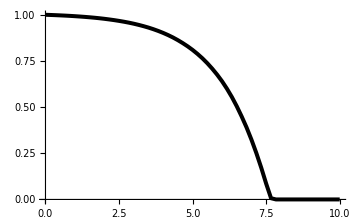

```mathematica
ListLinePlot[Transpose@{olks500kill[[All,1]],olks500kill[[All,2]]/56000},PlotStyle->{Thickness[0.008],Black},AxesStyle->Directive[Black, 16],ImageSize->Medium, Axes->{True,True}]
```

```mathematica
ListLinePlot[olks500typ[[1]],PlotStyle->{Thickness[0.008],RGBColor[1,0.36,0.36]},AxesStyle->Directive[Black, 16],ImageSize->Medium,PlotLegends->{"Protein"}]
```

-Graphics-

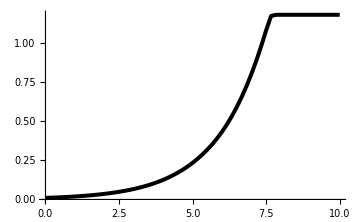

```mathematica
ListLinePlot[Transpose@{olks500kill[[All,1]],olks500kill[[All,19]]},PlotStyle->{Thickness[0.008],Black},AxesStyle->Directive[Black, 16],ImageSize->Medium, Axes->{True,True}]
```